```mathematica
n[n1_,n2_]:=Limit[(n1 m)/(n1+m),m->n2];
```

```mathematica
error[n1_,n2_]:=n1/n2
```

```mathematica
error[17,119]//N
```

0.142857

```mathematica
error[26,114]//N
```

0.22807

```mathematica
error[51,190]//N
```

0.268421

```mathematica
error[27,152]//N
```

0.177632

```mathematica
prob[n1_,n2_,dist_]:=
Block[{n,z,result},
n=Limit[(n1 m)/(n1+m),m->n2];
z=(√n+0.12+0.11/(√n))dist;

If[z==0,result=1,
If[z<1.18,Block[{y},
y=Exp[-1.23370055013616983/z^2];
result=1-2.25675833419102515 √(-Log[y])(y+y^9+y^25+y^49);
];,Block[{x},
x=Exp[-2 z^2];
result=2(x-x^4+x^9);
]]];
result
];
```

```mathematica
sigma[prob_]:=√2 InverseErf[1-prob];
```

```mathematica
sigma[prob[51,190,0.4]]
```

4.67488

```mathematica
sigma[prob[51,∞,0.4]]
```

5.35093

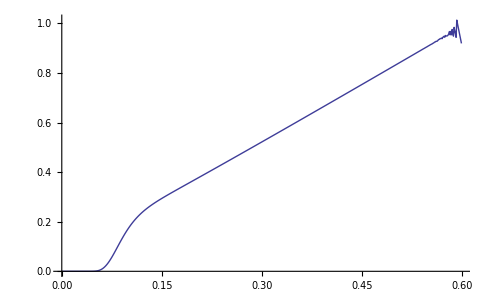

```mathematica
ListPlot[
Table[-sigma[prob[51,190,d]]+sigma[prob[51,∞,d]],{d,0,0.6,0.001}]
,DataRange->{0,0.6},Joined->True,PlotRange->All
]
```

```mathematica
prob[10,100,0.]
```

prob[10,100,0.]